Convolution of our dice

```mathematica
s={4,6,8,12,20};
```

```mathematica
ClearAll["`*"]
```

```mathematica
Subscript[pfX, 4][k_]:=Piecewise[{{1/4,1≤k≤4}}];
Subscript[pfX, 6][k_]:=Piecewise[{{1/6,1≤k≤6}}]
Subscript[pfX, 8][k_]:=Piecewise[{{1/8,1≤k≤8}}];
Subscript[pfX, 12][k_]:=Piecewise[{{1/12,1≤k≤12}}];
Subscript[pfX, 20][k_]:=Piecewise[{{1/20,1≤k≤20}}];
```

```mathematica
pfS[s_]:= Sum[pfX[x]*pfY[s-x],{x,0,12}];
```

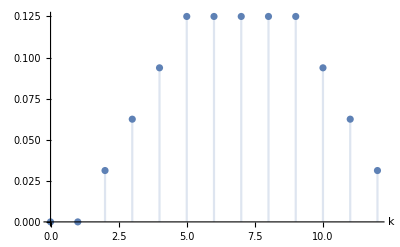

```mathematica
DiscretePlot[pfS[k],{k,0,12}, AxesLabel->Automatic]
```